# Type C orbit generator

## RNA, LOCAL MOVES ON PLANE TREES, AND TRANSPOSITIONS ON TABLEAUX

Professor Julianna Tymoczko

Laura Seegerer, Jennifer Tripp, and Judy Wang

Mathematics Department
Smith College

Created by Judy Wang: 17 April 2014
Last modified by Judy Wang: 09 January 2017

Mathematica 11.0.1.0 for Mac OS X x86 (64 bit)

## Number of plane trees

Using a theorem from Christine E. Heitsch’s paper “Combinatorics on plane trees, motivated by RNA secondary structure configurations” (http://people.math.gatech.edu/~heitsch/Pubs/plane.pdf), we can calculate the number of plane trees of different configurations.

### Number of plane trees

CountTrees takes in n and returns the number of plane trees with n edges.

```mathematica
(* Returns the total number of plane trees with n edges *)
CountTrees[n_]:=Module[{},
CatalanNumber[n]
];

(* Test *)
n=8;
Print["There are ",CountTrees[n]," plane trees with ",n," edges."]
```

There are 1430 plane trees with 8 edges.

### Number of symmetric plane trees

CountSymmetricTrees takes in n and returns the number of symmetric plane trees with n edges.

```mathematica
(* Returns all the multisubsets that sum to (n-m)/2 *)
Multisubsets[n_,m_]:=Module[
{L,newL},
L=Tuples[Range[0,(n-m)/2],m+1];
newL={};
For[i=1,i≤Length[L],i++,
If[Total[L[[i]]]==(n-m)/2,AppendTo[newL,L[[i]]],Null]
];
newL
];

(* Returns the sum of all the products of Catalan numbers *)
SumOfCatalanProducts[L_]:=Module[
{product,sum},
sum=0;
For[i=1,i≤Length[L],i++,
product=1;
For[j=1,j≤Length[L[[i]]],j++,
product*=CatalanNumber[L[[i]][[j]]];
];
sum+=product;
];
sum
];

(* Returns the total number of symmetric plane trees with n edges *)
CountSymmetricTrees[n_]:=Module[
{m,L,sum},
sum=0;
For[r=0,r≤Floor[n/2],r++,
m=2*r+Mod[n,2];
L=Multisubsets[n,m];
sum+=SumOfCatalanProducts[L];
];
sum
];

(* Test: *)
n=8;
Print["There are ",CountSymmetricTrees[8]," symmetric plane trees with ",n," edges."];
```

There are 70 symmetric plane trees with 8 edges.

### Number of asymmetric plane trees

CountAsymmetricTrees takes in n and returns the number of asymmetric plane trees with n edges.

```mathematica
(* Returns the total number of asymmetric plane trees with n edges *)
CountAsymmetricTrees[n_]:=Module[{},
CountTrees[n]-CountSymmetricTrees[n]
];

(* Test: *)
n=8;
Print["There are ",CountAsymmetricTrees[n]," asymmetric plane trees with ",n," edges."];
```

There are 1360 asymmetric plane trees with 8 edges.

## Functions

```mathematica
(* Load graph utilities for orbit arrow options *)
<<GraphUtilities`
```

### Permutation groups

#### Weyl group C_n

This function outputs all the elements of C_n.

```mathematica
(* Outputs all elements of Subscript[C, n] in disjoint cycle notation. *)
Cn[n_]:=
Module[{length,bigList,list,test,cycles},
(* All permutations *)
length=2 n;
bigList=Permutations[Table[i,{i,length}],{length}];

(* Select only permutations whose entries are fully reflected to the other side of the mirror *)
list={};
For[ii=1,ii≤Length[bigList],ii++,
test=0;
For[j=1,j≤length/2,j++,
If[bigList[[ii]][[j]]+bigList[[ii]][[length-j+1]]==length+1,test++]];
If[test==length/2,list=Append[list,bigList[[ii]]]]];

(* Convert from 1-line notation into disjoint cycle notation *)
cycles={};
For[ii=1,ii≤Length[list],ii++,
AppendTo[cycles,PermutationCycles[list[[ii]]]]];
cycles];
```

This function outputs all the generators of C_n.

```mathematica
(* Outputs the list of all the generators for Subscript[C, n] in the form of 
"{Cycles[{{1,2},{5,6}}],Cycles[{{2,3},{4,5}}],Cycles[{{3,4}}]}" in Subscript[C, 3]. *)
CnGenerators[n_]:=Table[If[i==n,Cycles[{{i,i+1}}],
Cycles[{{i,i+1},{2n-i,2n-i+1}}]],{i,n}];
```

#### Weyl group D_n

This function outputs all the elements of D_n.

```mathematica
(* Outputs all elements of Subscript[D, n] in disjoint cycle notation. *)
Dn[n_]:=Module[{length,bigList,midList,list,test,cycles},
(* All permutations *)
length=2 n;
bigList=Permutations[Table[i,{i,length}],{length}];

(* Select only permutations whose entries are fully reflected to the other side of the mirror *)
midList={};
For[i=1,i<=Length[bigList],i++,
test=0;
For[j=1,j≤length/2,j++,
If[bigList[[i]][[j]]+bigList[[i]][[length-j+1]]==length+1,test++]];
If[test==length/2,midList=Append[midList,bigList[[i]]]]];

(* Select only the permutations who has an even number of entries with value greater than the mirror *)
list={};
For[i=1,i<=Length[midList],i++,
test=0;
For[j=1,j≤length/2,j++,
If[midList[[i]][[j]]>length/2,test++]]
If[Mod[test,2]==0,list=Append[list,midList[[i]]]]];

(* Convert from 1-line notation into disjoint cycle notation *)
cycles={};
For[ii=1,ii≤Length[list],ii++,
AppendTo[cycles,PermutationCycles[list[[ii]]]]];
cycles];
```

This function outputs all the generators of D_n.

```mathematica
(* Outputs the list of all the generators for Subscript[D, n] in the form of "{Cycles[{{1,2},{5,6}}],Cycles[{{2,3},{4,5}}],Cycles[{{2,5},{3,4}}]}" in Subscript[D, 3]. *)
DnGenerators[n_]:=Table[If[i==n,Cycles[{{i,i+1},{i-1,i+2}}],
Cycles[{{i,i+1},{2n-i,2n-i+1}}]],{i,n}];
```

### Plane Trees

#### Convert Young tableau into plane tree

This function converts a Young tableau into a plane tree.
Used in TreeAndTableau.

```mathematica
(* Converts a Young tableau into a plane tree. Used in TreeAndTableau. *)
TableauToTree[y_]:=Module[
{n,toprow,
start,end,diff,
iList,jList,masterList,
newi,newj,iLast,jLast,masterLast,edge,tempList,
nodesize},

nodesize = 2; (* Size of tree nodes *)

toprow=y[[1]]; (* Top row of the Young tableau *)
start=1; (* Array position of the starting vertex of a directed edge *)
end=2;  (* Array position of the ending vertex of a directed edge *)
n=Length[toprow]; (* Length of Young tableau *)
iList={1->2}; (* List of downward edges *)
jList={}; (* List of upward edges *)
masterList=iList; (* List of both doward and upward edges *)

(* Outer for loop starts *)
For[ii=1,ii<n,ii++,
diff=toprow[[ii+1]]-toprow[[ii]]; (* Difference between an entry in the top row and the next entry in the top row *)
(* If diff == 1 *)
If[diff==1,
iLast=Last[iList];
newi=iLast[[end]]-> iLast[[end]]+1;
AppendTo[iList,newi];
AppendTo[masterList,newi],
(* If diff ≠ 1 *)
(* Search for the first element in masterList whose end point is greater than start point, then reverse the start and end points *)
edge=Last[masterList];
newj=edge[[end]]->edge[[start]];
tempList={newj};

(* Inner for loop starts *)
For[jj=1,jj≤Length[masterList],jj++,
If[Length[tempList]==diff-1,Break[]];
edge=masterList[[-jj]];
If[edge[[end]]>edge[[start]]&&edge[[end]]==newj[[end]],
newj=edge[[end]]->edge[[start]];
AppendTo[tempList,newj]]]; (* Inner for loop ends *)

jList=Join[jList,tempList];
masterList=Join[masterList,tempList];
newi=Last[jList][[end]]-> Last[iList][[end]]+1; (* One downward half edge *)
AppendTo[iList,newi];
AppendTo[masterList,newi]]]; (* Outer for loop ends *)

(* j-edge incident to last leaf *)
diff=n-Last[toprow];
edge=Last[masterList];
newj=edge[[end]]->edge[[start]];
tempList={newj};

(* For loop starts *)
For[jj=1,jj≤Length[masterList],jj++,
If[Length[tempList]==diff-1,Break[]];
edge=masterList[[-jj]];
If[edge[[end]]>edge[[start]]&&edge[[end]]==newj[[end]],
newj=edge[[end]]->edge[[start]];
AppendTo[tempList,newj]]]; (* For loop ends *)

jList=Join[jList,tempList];
masterList=Join[masterList,tempList];

(* Show function starts *)
Show[
(* TreePlot function starts *)
TreePlot[iList,Automatic,1,
ImageSize->{45,45},
LayerSizeFunction->(1&),
VertexLabeling->False,
DirectedEdges->False,
(* Make edges black *)
EdgeRenderingFunction->( {Black,Line[#]} &),
(* Make root white and other nodes black *)
VertexRenderingFunction->(
If[#2==1,
{White,EdgeForm[Black],Disk[#,Offset[{nodesize,nodesize}]]},
{Black,EdgeForm[Black],Disk[#,Offset[{nodesize,nodesize}]]}
]
&)] (* TreePlot function ends *)
](* Show function ends *)
];

(* Test: *)
(*
TableauToTree[{{1,2,4,5,7,11,12,15,16,18,19,21,25},{3,6,8,9,10,13,17,20,22,23,24,26}}];
TableauToTree[{{1,2,3,5,9,10},{4,6,7,8,11,12}}];
TableauToTree[{{1,2,3},{4,5,6}}];
*)
```

#### Display plane tree with Young tableau

This function displays a plane tree with associated Young tableau. 
Used in Orbit and Orbits.

```mathematica
(* Displays a plane tree with associated Young tableau. Used in Orbit and Orbits. *)
TreeAndTableau[y_]:=Module[{tableau,tree},
tableau=Grid[y,Frame->All,Alignment->{Center,Center}];
tree=TableauToTree[y];
Grid[{{tree},{tableau}},Spacings->{0.5,0.5},Frame->All,FrameStyle->Opacity[0]]];

(* Test: *)
(*
TreeAndTableau[{{1,2,3},{4,5,6}}];
TreeAndTableau[{{1,3,5},{2,4,6}}];
*)
```

### Young tableaux

#### Convert tabloid to tableau

This function rearranges a tabloid into a Young tableau. 
Used in PermuteTableau and Tableaux.

```mathematica
(* Rearranges a tabloid into a Young tableau. Used in PermuteTableau and Tableaux. *)
TabloidToTableau[y_]:=Module[{height,length,yrow,yTrans,ycol,ynew},
height=Length[y];
length=Length[y[[1]]];
yrow=Table[Sort[y[[i]]],{i,height}]; (* Orders all the rows *)
yTrans=Transpose[yrow];
ycol=Table[Sort[yTrans[[i]]],{i,length}]; (* Orders all the rows *)
ynew=Transpose[ycol]];
```

#### Generate Young tableaux

This function generates all the distinct n×m standard Young tableaux. 

For m=2, the function can handle n-values up to 5 before crashing:
n = 1 took 0.084986 seconds;
n = 2 took 0.097173 seconds;
n = 3 took 0.36177 seconds;
n = 4 took 3.84622 seconds;
n = 5 took 257.013 seconds;
n = 6 crashes.

Used as input for orbit-generating functions.

```mathematica
(* Generates all the distinct n × m Young tableaux, where n is width and m is height. 
Used as input for orbit-generating functions. *)
(* 
Each Young tableau is expressed as {{a, b, c},{d, e, f},...}, 
with {a, b, c} representing the top row, 
{d, e, f} representing the lower row, 
etc. 
*)
Tableaux[n_,m_]:=Module[{allperm,allpartperm,allY},
allperm=Permutations[Table[i,{i,n*m}]];
allpartperm=Table[Partition[allperm[[i]],n],{i,(n*m)!}];
allY=Table[TabloidToTableau[allpartperm[[i]]],{i,(n*m)!}] ;
DeleteDuplicates[allY]];

(* Test: *)
(* Tableaux[3,3] *)
```

This function generates all the distinct n×2 standard Young tableaux. 

More efficient than Tableaux, nBy2Tableaux can handle n-values up to 7 before crashing:
n = 1 took 0.022711 seconds;
n = 2 took 0.074025 seconds;
n = 3 took 0.240827 seconds;
n = 4 took 1.21538 seconds;
n = 5 took 3.76734 seconds;
n = 6 took 24 seconds;
n = 7 took 257 seconds;
n = 8 crashes.

Used as input for orbit-generating functions.

```mathematica
(* Generates all the distinct n × 2 standard Young tableaux, where n is width and 2 is height. 
Used as input for orbit-generating functions. *)
(* 
Each Young tableau is expressed as {{a, b, c},{d, e, f}}, 
with {a, b, c} representing the top row and {d, e, f} representing the bottom row. 
*)
nBy2Tableaux[n_]:=Module[{universe,toprows,tabloids,columns,tableaux},
(* Ground set *)
universe = Range[2*n];
(* All possible top rows *)
toprows=Permutations[universe,{n}];
(* Sort top rows *)
toprows=Table[Sort[toprows[[i]]],{i,Length[toprows]}];
(* Remove duplicate top rows *)
toprows=DeleteDuplicates[toprows];
(* Construct tabloids *)
tabloids = Table[{toprows[[i]],Complement[universe,toprows[[i]]]},{i,Length[toprows]}];
(* Tabloids by column *)
columns = Table[Transpose[tabloids[[i]]],{i,Length[tabloids]}];
(* Sort columns *)
columns = Table[Table[Sort[columns[[i]][[j]]],{j,Length[columns[[i]]]}],{i,Length[columns]}];
(* Remove duplicate columns *)
columns=DeleteDuplicates[columns];
(* Remove duplicate tableaux *)
tableaux=Table[Transpose[columns[[i]]],{i,Length[columns]}];
(* Output standard Young tableaux *)
tableaux
];

(* Test: *)
(* nBy2Tableaux[3] *)
```

#### Apply permutations to Young tableau

This function matches each numeric entry in cycle_ to the corresponding element in list_ and outputs a cycle in the form of the elements’ positions in list_. 
Used in PermuteTableau.

```mathematica
(* Matches each numeric entry in cycle_ to the corresponding element in list_and 
outputs a cycle in the form of the elements' positions in list_. Used in PermuteTableau. *)
IndexForm[list_,cycle_]:=Module[{newcycle},
newcycle={};
(* Outer for loop starts *)
For[ii=1,ii≤Length[cycle],ii++,
(* Inner for loop starts *)
For[j=1,j≤Length[list],j++,
If[cycle[[ii]]==list[[j]],AppendTo[newcycle,j]]
] (* Inner for loop ends *)
]; (* Outer for loop ends *)
Cycles[{newcycle}]];

(* Test: *)
(*
IndexForm[{1,4,3,2},{2,3}] 
*)
```

This function applies a permutation to a Young tableau. 
Used in Orbit and Orbits.

```mathematica
(* Applies a permutation to a Young tableau. perm_ takes the form of "Cycles[{{a, b},{c, d},{e, f, g}}]." Used in Orbits. *)
PermuteTableau[y_,perm_]:=Module[{newList,cycles},
(* Number of cycles in a permutation *)
cycles=Length[perm[[1]]]; 
newList=Flatten[y];
(* Applies permutation to list *)
For[k=1,k≤cycles,k++,
newList=Permute[newList,IndexForm[newList,perm[[1]][[k]]]]
]; 
newList=Partition[newList,Length[y[[1]]]];
TabloidToTableau[newList] 
];
```

### Orbits

#### Format edge labels

This function takes an involution in cycle notation (e.g. {{1,2}}) and permutation type (e.g. “C”) and outputs the involution in s_i-local move notation (e.g. s_i^C). The output will be used as edge labels in an orbit.
Used in Orbit and Orbits.

```mathematica
(* Takes an involution in cycle notation (e.g.{{1,2}}) and permutation type (e.g. "C") and outputs the involution in local move notation (e.g. Subscript[s, 1]^C). Used in Orbit and Orbits. *)
FormatLocalMove[perm_,type_]:=Module[{localmove,involutions,label},
Which[
(* ******************************************** *)
type == "A",
involutions="";
For[ii=1,ii≤Length[perm],ii++,
involutions = involutions Subscript["s",First[perm[[ii]]]]
];
label=Style[involutions,Italic,Small],

(* ******************************************** *)
type== "C",
localmove=Subsuperscript["s",First[perm[[1]]],type];
label=Style[localmove,Italic,Small]
];
label
];

(* Test: *)
(* FormatLocalMove[{{1,2}},"C"] *)
```

#### Find one orbit

This functions takes a Young tableau and a permutation group and outputs the orbit that the Young tableau is in.

```mathematica
(* Finds the orbit tableau_ is in. *)
Orbit[tableau_,permutations_,multigraph_:False]:=Module[
{
type,scale,
parent, parents,child,children,childless,
downstream,upstream,label,
orbit
},

(* Extract the type letter of the given permutation group *)
type=StringPart[ToString[permutations],2];
(* Scaling unit *)
scale=Length[permutations];

parent=tableau;
parents={};
child={};
children={};
childless=False;
orbit={};

(* While loop starts *)
While[!childless,
AppendTo[parents,parent];

(* For loop starts *)
For[qq=1,qq≤ Length[permutations],qq++,
child=PermuteTableau[parent,permutations[[qq]]];

label = StandardForm[FormatLocalMove[permutations[[qq]][[1]],type]];
downstream = {TreeAndTableau[parent]->TreeAndTableau[child],label};
upstream = {TreeAndTableau[child]->TreeAndTableau[parent],label};

(* Determine if the orbits would include multi-edges or not. *)
If[multigraph,
AppendTo[orbit,downstream];
arrowhead=Small,

If[MemberQ[orbit, upstream],,AppendTo[orbit,downstream]];
arrowhead=0
];

AppendTo[children,child];
]; (* For loop ends *)

children=DeleteDuplicates[children];
children=Complement[children,parents];  (* Removes from children anything that is in parents *)
If[children=={},childless=True,parent=children[[1]]];
]; (* While loop ends *)

(* Print function *)
Print[LayeredGraphPlot[orbit,Top,
SelfLoopStyle->None,
DirectedEdges->False,
PlotRangePadding->None,
VertexLabeling->True,
Background->White,
BaseStyle->{FontWeight->"Plain"},
PackingMethod->"ClosestPacking",
AspectRatio->Automatic,
ImageSize->-900+1579 n-693 n^2+97 n^3,
VertexRenderingFunction->({Background->White,Text[#2,#1]}&),
EdgeRenderingFunction->
({
Arrowheads[arrowhead],
Arrow[#1,-0.5+0.5 n-0.1 n^2],
Text[#3,LineScaledCoordinate[#1,0.475],Background->White]
}&)
]] (* End of print function *)
]; 

(* Test: *)
(* Orbit[{{1,2,3},{4,5,6}},CnGenerators[3]] *)
(* Orbit[{{1,2,4},{3,5,6}},CnGenerators[3]] *)
(* Orbit[{{1,2,3,4},{5,6,7,8}},CnGenerators[4]] *)
(* Orbit[{{1,2,3,4,5},{6,7,8,9,10}},CnGenerators[5]] *)
(* Orbit[{{1,2,3,4,8},{5,6,7,9,10}},CnGenerators[5]] *)
(* Orbit[{{1,2,5,6,8},{3,4,7,9,10}},CnGenerators[5]] *)
(* Orbit[{{1,2,3,4,5,6,7,8},{9,10,11,12,13,14,15,16}},CnGenerators[8]] *)
```

#### Find all orbits

This function finds all the orbits of a group.

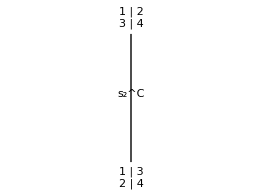

{0.084079,Null}

```mathematica
(* Finds all the orbits of a group. 
To label the edges correctly, permutations_ must begin with the letter for the type of the given permutation group.
Set multigraph_ to True to include multi-edges. 
Set multigraph_ to False to prevents multi-edges. *)
Orbits[tableaux_,permutations_,multigraph_:False]:=Module[
{
type,n,
orphans,parent,parents,child,children,childless,
downstream,upstream,label,
orbit, orbits,
arrowhead
},
 
(* Extract type letter of the given permutation group *)
type=StringPart[ToString[permutations],2];
n=Length[permutations];

orphans=tableaux;
orbits={};

(* Find all orbits *)
(* Start of outer while loop *)
While[orphans≠{},
parent=orphans[[1]];
parents={};
child={};
children={};
childless=False;
orbit={};

(* Find one orbit *)
(* Start of inner while loop *)
While[!childless,
AppendTo[parents,parent];
(* Start of for loop *)
For[qq=1,qq≤ Length[permutations],qq++,
child=PermuteTableau[parent,permutations[[qq]]];
label = StandardForm[FormatLocalMove[permutations[[qq]][[1]],type]];
downstream = {TreeAndTableau[parent]->TreeAndTableau[child],label};
upstream = {TreeAndTableau[child]->TreeAndTableau[parent],label};

(* Determine if the orbits would include multi-edges or not. *)
If[multigraph,
AppendTo[orbit,downstream];
arrowhead=Small,

If[MemberQ[orbit, upstream],,AppendTo[orbit,downstream]];
arrowhead=0
];

AppendTo[children,child];
]; (* End of for loop *)
children=DeleteDuplicates[children];
children=Complement[children,parents];  (* Removes from children anything that is in parents *)
If[children=={},childless=True,parent=children[[1]]];
]; (* End of inner while loop *)
orphans= Complement[orphans,parents];
orbits=Catenate[{orbits,orbit}];
]; (* End of outer while loop *)

(* Print function *)
Print[LayeredGraphPlot[orbits,Top,
SelfLoopStyle->None,
DirectedEdges->False,
PlotRangePadding->None,
VertexLabeling->True,
Background->White,
BaseStyle->{FontWeight->"Plain"},
PackingMethod->"ClosestPacking",
AspectRatio->Automatic,
ImageSize->-900+1579 n-693 n^2+97 n^3,
VertexRenderingFunction->({Background->White,Text[#2,#1]}&),
EdgeRenderingFunction->
({
Arrowheads[arrowhead],
Arrow[#1,-0.5+0.5 n-0.1 n^2],
Text[#3,LineScaledCoordinate[#1,0.475],Background->White]
}&)
]] (* End of print function *)
]; 

(* Test: *)
(* n=4;  Timing[Orbits[nBy2Tableaux[n],CnGenerators[n]]] *)
n=2; Timing[Orbits[nBy2Tableaux[n],CnGenerators[n]]]
```

### Resize graphics

The visual size of an orbit can vary wildly with respect to n. We try to output graphics that are easier to read by using a polynomial fit to approximate the relationship between ImageSize or arrow setback and n. The following two sections produce the polynomial fits we seek.

#### ImageSize

-900.+1578.77 n-692.56 n^2+96.5278 n^3

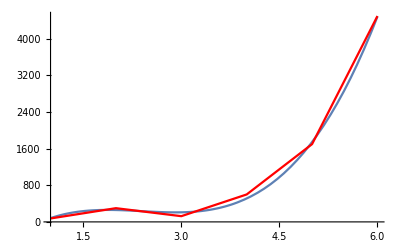

```mathematica
(* ImageSize *)
Clear[n];
p1=75;
p2=300;
p3=125;
p4=600;
p5=1700;
p6=4500;
dataline=ListLinePlot[{p1,p2,p3,p4,p5,p6},AxesLabel->Automatic,PlotStyle->Red];
data={{1,p1},{2,p2},{3,p3},{4,p4},{5,p5},{6,p6}};
fitline=Fit[data,{1,n,n^2,n^3},n]
Show[Plot[fitline,{n,1,6}],dataline]
```

#### Arrow

-0.475+0.515833 n-0.1025 n^2+0.00666667 n^3

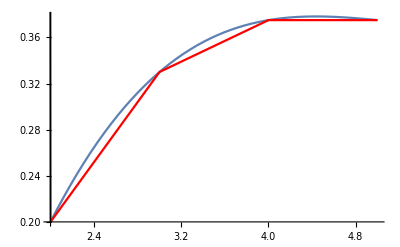

```mathematica
(* Arrow setback distance *)
Clear[n];
p2=0.2;
p3=0.33;
p4=0.375;
p5=0.375;
dataline=ListLinePlot[{p1,p2,p3,p4,p5},AxesLabel->Automatic,PlotStyle->Red];
data={{2,p2},{3,p3},{4,p4},{5,p5}};
fitline=Fit[data,{1,n,n^2,n^3},n]
Show[Plot[fitline,{n,2,5}],dataline]
```

## Apply C_n to Young tableaux

### Orbits in C_1

```mathematica
(* 
n=1; Timing[Orbits[nBy2Tableaux[n],CnGenerators[n]]]   
*)
n=1; Timing[Orbits[nBy2Tableaux[n],CnGenerators[n]]]
```

-Graphics-

{0.025193,Null}

### Orbits in C_2

```mathematica
(* 
n=2; Timing[Orbits[nBy2Tableaux[n],CnGenerators[n]]]  
*)
n=2; Timing[Orbits[nBy2Tableaux[n],CnGenerators[n]]]
```

-Graphics-

{0.074034,Null}

### Orbits in C_3

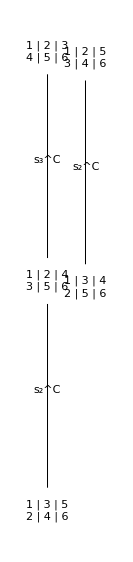

{0.238802,Null}

```mathematica
(* 
n=3; Timing[Orbits[nBy2Tableaux[n],CnGenerators[n]]] 
*)
n=3; Timing[Orbits[nBy2Tableaux[n],CnGenerators[n]]]
```

### Orbits in C_4

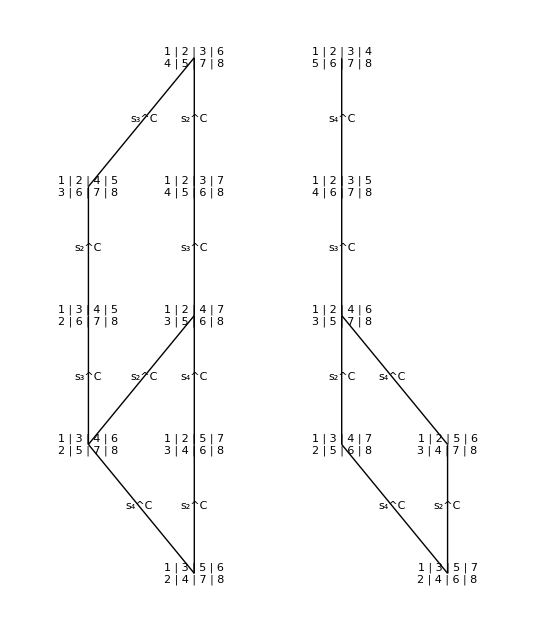

{0.871578,Null}

```mathematica
(* 
n=4; Timing[Orbits[nBy2Tableaux[n],CnGenerators[n]]] 
*)
n=4; Timing[Orbits[nBy2Tableaux[n],CnGenerators[n]]]
```

### Higher-order orbits

Tableaux:
n = 1 took 0.084986 seconds
n = 2 took 0.097173 seconds
n = 3 took 0.36177 seconds
n = 4 took 3.84622 seconds
n = 5 took 257.013 seconds
n = 6 crashes

nBy2Tableaux:
n = 1 took 0.022711 seconds
n = 2 took 0.074025 seconds
n = 3 took 0.240827 seconds
n = 4 took 1.21538 seconds
n = 5 took 3.76734 seconds
n = 6 took 24 seconds
n = 7 took 257 seconds
n = 8 crashes

```mathematica
(* 
n = 5; Timing[Orbits[nBy2Tableaux[n],CnGenerators[n]]] 
*)
```

## Scratch work